# Math 223: Homework 9

Maia Powell

9 April 2021

## Problem 1

#### Use second-order perturbation theory to find approximations to the roots of x^2+x+6ε =0.

(∑_(n=0)^∞ x_n ϵ^n)^2+(∑_(n=0)^∞ x_n ϵ^n)+6ϵ = 0

```mathematica
SeriesCoefficient[Series[(Sum[x[n] ϵ^n,{n,0,10}])^2+Sum[x[n] ϵ^n,{n,0,10}]+6ϵ,{ϵ,0,2}],0]
```

x[0]+x[0]^2

```mathematica
Solve[x[0]+x[0]^2==0,x[0]]
```

{{x[0]→-1},{x[0]→0}}

```mathematica
SeriesCoefficient[Series[(Sum[x[n] ϵ^n,{n,0,10}])^2+Sum[x[n] ϵ^n,{n,0,10}]+6ϵ,{ϵ,0,2}],1]/.x[0]->-1
```

6-x[1]

```mathematica
Solve[6- x[1]==0,x[1]]
```

{{x[1]→6}}

```mathematica
SeriesCoefficient[Series[(Sum[x[n] ϵ^n,{n,0,10}])^2+Sum[x[n] ϵ^n,{n,0,10}]+6ϵ,{ϵ,0,2}],2]/.{x[0]->-1,x[1]->6}
```

36-x[2]

```mathematica
Solve[36- x[2]==0,x[ 2]]
```

{{x[2]→36}}

x=-1+6ϵ +36 ϵ^2+O(ϵ^3)

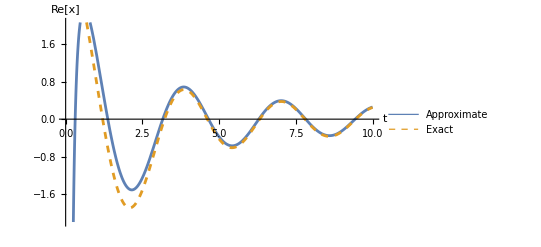

```mathematica
Plot[{Re[1/(ⅈ*x)(Sin[2]+2)ⅇ^(2ⅈ*x)]+Re[1/x^2((Cos[2]+1)ⅇ^(2ⅈ*x)-Cos[0])], Re[NIntegrate[((Sin[t])+t)ⅇ^(ⅈ*x*t), {t,0,2}]]},{x,0,10},PlotStyle-> {Directive[Solid,Thickness[0.005]], Directive[Dashed,Thickness[0.005]]},AxesLabel->{Style["t",Italic,18],Style["Re[x]", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Approximate","Exact"}]
```

## Problem 2

#### Compute all of the coefficients in the perturbation series solution to the initial-value problem y'=y+ε xy, y(0)=1 Show that the series converges for all values of ε. Also, compute the perturbation series indirectly by expanding the explicit exact solution in powers of ε.

```mathematica
DSolve[{Subscript[y, 0]'[x]-Subscript[y, 0][x]==0,Subscript[u, 0][0]==1},Subscript[u, 0][x],x]
```

## Problem 3

#### Show that the solution to the initial-value problem y''+y+ε y=0, y'(0)=0 remains bounded for all real x. Obtain a first-order perturbative approximation to y(x) and show that it is unbounded as x→∞. Conclude that the first-order approximation is valid only for |x|< O(ε^-1).